```mathematica
v[t]/.DSolve[{v'[t]==-k v[t],v[0]==v0},v[t],t][[1]]
```

ⅇ^(-k t) v0

```mathematica
Integrate[%4,{t,0,t}]
```

(v0-ⅇ^(-k t) v0)/k

```mathematica
x[t_,k_,v0_]:=(v0-ⅇ^(-k t) v0)/k;
```

```mathematica
Limit[%11,t->Infinity]
```

ConditionalExpression[v0/k, v0∈ℝ&&k>0]

```mathematica
x[t,1,5]
```

5-5 ⅇ^-t

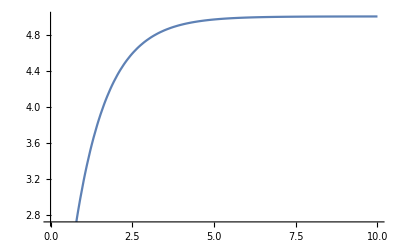

```mathematica
Plot[x[t,1,5],{t,0,10}]
```

```mathematica
Manipulate[
DiscretePlot[(Binomial[kTotal,k]Binomial[total-kTotal,n-k])/Binomial[total,n],{k,0,total}],
{total,0,100,1},
{kTotal,0,100,1},
{n,0,100,1}
]
```

```mathematica
(n+1)(kTotal+1)/(total+2)/.{n->11,kTotal->5,total->15}//N
```

4.23529

```mathematica
Manipulate[
DiscretePlot[Binomial[n,k] p^k(1-p)^(n-k),{k,0,20}],
{p,0,1},
{n,0,100,1}
]
```

```mathematica
Manipulate[
DiscretePlot[Binomial[n,k] p^k(1-p)^(n-k),{n,0,100}],
{p,0,1},
{k,0,100,1}
]
```

```mathematica
v0=12
```

```mathematica
u=10
```

10

```mathematica
g=10
```

10

```mathematica
a=2
```

2

```mathematica
Clear[a,g,u,v0]
```

```mathematica
DSolve[{
vx[0]==v0,
vy[0]==0,
vx'[0]==0,
vy'[0]==g Sin[a],
vx'[t]==-(u g Cos[a] vx[t])/(√(vx[t]^2+vy[t]^2)),
vy'[t]==-(u g Cos[a] vy[t])/(√(vx[t]^2+vy[t]^2))+g Sin[a]
},{vx[t],vy[t]},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

```mathematica
(7+√50)^(1/3)+(7-√50)^(1/3)//FullSimplify
```

2